```mathematica
Clear["Global`*"]
Needs["Developer`"]
Needs["CCompilerDriver`"]
```

## Dumping and Reading .msh File - Modular

```mathematica
Needs["Developer`"]
```

```mathematica
ClearAll[ReadMSHFile,DumpMSHFileTo2DATFiles,ReadMSHFileFrom2DATFiles]
ReadMSHFile[filename_]:=Module[{i,SkipStreamNumbers,ReadStreamNumbers,meshStr,nNodes,nodesTable,nElements,nPoints,nLines,nTriangles,trianglesTable,temp},
SkipStreamNumbers=Skip[#1,Table[Number,{i,Range[#2]}]]&;
ReadStreamNumbers=Read[#1,Table[Number,{i,Range[#2]}]]&;
meshStr=OpenRead[filename];
Find[meshStr,"$Nodes"];
nNodes=Read[meshStr,Number];
nodesTable=ConstantArray[0.0,{nNodes,2}];
For[i=1,i≤nNodes,i++,
Skip[meshStr,Number];
nodesTable⟦i⟧=N@ReadStreamNumbers[meshStr,2];
Skip[meshStr,Number];
];
Find[meshStr,"$Elements"];
nElements=Read[meshStr,Number];
nPoints=0;nLines=0;nTriangles=0;
trianglesTable=ConstantArray[0.0,{nElements,3}];
For[i=1,i≤nElements,i++,
Skip[meshStr,Number];
temp=Read[meshStr,Number];
If[temp==15,nPoints++;SkipStreamNumbers[meshStr,4];];
If[temp==1,nLines++;SkipStreamNumbers[meshStr,5];];
If[temp==2,nTriangles++;SkipStreamNumbers[meshStr,3];trianglesTable⟦nTriangles⟧=N@ReadStreamNumbers[meshStr,3];];
];
trianglesTable=trianglesTable⟦1;;nTriangles⟧;
Close[meshStr];
ToPackedArray/@{nodesTable,Floor@trianglesTable}
]
DumpMSHFileTo2DATFiles[mshfilename_]:=Module[{dir,nodesTable,trianglesTable},
{nodesTable,trianglesTable}=ReadMSHFile[mshfilename];
dir=FileNameJoin[{DirectoryName[mshfilename],FileBaseName[mshfilename]<>".dat"}];
CreateDirectory[dir]//Quiet;
Print["directory created:",dir];
Export[FileNameJoin[{dir,"nodes.dat"}],nodesTable];
Export[FileNameJoin[{dir,"triangles.dat"}],trianglesTable];
Print["exported nodes file: ",FileNameJoin[{dir,"nodes.dat"}]];
Print["exported triangles file: ",FileNameJoin[{dir,"triangles.dat"}]];
]
ReadMSHFileFrom2DATFiles[mshfilename_]:=Module[{dir},
dir=FileNameJoin[{DirectoryName[mshfilename],FileBaseName[mshfilename]<>".dat"}];
Print["imported nodes file: ",FileNameJoin[{dir,"nodes.dat"}]];
Print["imported triangles file: ",FileNameJoin[{dir,"triangles.dat"}]];
ToPackedArray/@{N@Import[FileNameJoin[{dir,"nodes.dat"}]],Import[FileNameJoin[{dir,"triangles.dat"}]]}
]
```

Read directly from the .msh file and check

```mathematica
dir=FileNameJoin[{NotebookDirectory[],"../msh"}]
```

/home/qzmfrank/codes/rte2dvis/notebook/../msh

```mathematica
{nodesRaw,trianglesRaw}=ReadMSHFile[FileNameJoin[{dir,"square26.msh"}]];
PackedArrayQ/@{nodesRaw,trianglesRaw}
```

{True,True}

Dump the .msh file data into two separate .dat files

```mathematica
DumpMSHFileTo2DATFiles[FileNameJoin[{dir,"square26.msh"}]]
```

directory created:/home/qzmfrank/codes/rte2dvis/notebook/../msh/square26.dat

exported nodes file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square26.dat/nodes.dat

exported triangles file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square26.dat/triangles.dat

Read the two .dat files and check

```mathematica
{nodesRaw2,trianglesRaw2}=ReadMSHFileFrom2DATFiles[FileNameJoin[{dir,"square26.msh"}]];
PackedArrayQ/@{nodesRaw2,trianglesRaw2}
Total[Norm/@#]&/@{nodesRaw2-nodesRaw,trianglesRaw2-trianglesRaw}
```

imported nodes file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square26.dat/nodes.dat

imported triangles file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square26.dat/triangles.dat

{True,True}

{0.,0}

## Direct Integral Solver - Sequential, Interpretive and Partially Compiled

```mathematica
Needs["Developer`"]

ClearAll[filename,mus,mua,mut,g,Phasef,Phasef1,Phasef2,PhaseFunc,PhaseFunc1,phis,Nd]
(*filename=FileNameJoin[{NotebookDirectory[],"../msh","t4.msh"}];*)
filename=FileNameJoin[{NotebookDirectory[],"../msh","square162.msh"}];
DumpMSHFileTo2DATFiles[filename];
(*
mus[{x_,y_}]:=2x^2+y+Exp[-0.1x-0.2y]
mua[{x_,y_}]:=x+3y^2-Exp[-0.5x+y^2]
*)
mus[{x_,y_}]:=2Log[2]
mua[{x_,y_}]:=Log[2]
mut[{x_,y_}]:=mua[{x,y}]+mus[{x,y}]
g=0.6;
Phasef1[m_]:=g^Abs[m]
Phasef2[m_]:=If[m==0,1.0,0.0]
Phasef=Phasef1;
PhaseFunc1=Compile[{{phi,_Real}},(1.0-g^2)/(2π(1+g^2-2g Cos[phi]))(*,CompilationTarget:>"C"*)];
PhaseFunc=PhaseFunc1;
phis=0;
Nd=50;

ClearAll[iG,iL,Rank,ToCmplxPckdArry]
iG[{n_,m_},{Ns_,Nd_}]:=(n-1)*(2Nd+1)+m+Nd+1
iL[ng_,{Ns_,Nd_}]:={IntegerPart[(ng-1)/(2Nd+1)+1],Mod[ng-Nd-1,(2Nd+1),-Nd]}
Rank[x_]:=Length/@{x,xᵀ}//Quiet
ToCmplxPckdArry=ToPackedArray[N[Re[#]]]+ⅈ ToPackedArray[N[Im[#]]]&;

ClearAll[TriPtPreCalc,CntrPreCalc,r2rXYPreCalc,r2rRPreCalc,r2rPhiPreCalc,r2rFPreCalc,SignedAreaPreCalc]
TriPtPreCalc[p_,t_]:=p⟦#⟧&/@t//ToPackedArray
CntrPreCalc[pt_]:=(Total/@pt)/3.0//ToPackedArray
RcPreCalc[pt_]:=With[{a=Norm[#⟦1⟧-#⟦2⟧];b=Norm[#⟦1⟧-#⟦2⟧];c=Norm[#⟦1⟧-#⟦2⟧];},s=0.5(a+b+c);(a b c)/Sqrt[s(s-a)(s-b)(s-c)]]&/@pt
r2rRPreCalc[cntr_]:=Outer[If[#1<#2,Norm[Subtract@@cntr⟦{#1,#2}⟧],0.0]&,Range[Length[cntr]],Range[Length[cntr]]]//ToPackedArray//#+#ᵀ&
SignedAreaPreCalc[pt_]:=pt//Map[{#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦3⟧}&,#]&//Map[#⟦1,1⟧#⟦2,2⟧-#⟦1,2⟧#⟦2,1⟧&,#]&//ToPackedArray//Times[#,0.5]&;

ClearAll[Np,p,t,Nn,Nm,Ns,Ng,gTbl,iGTbl,iLTbl,pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,signedArea,area,Rc,Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,Tarea,TRc,musTbl,muaTbl,mutTbl]
{p,t}=ReadMSHFileFrom2DATFiles[filename];

(*
(*symmetrize the geometry w.r.p.t. y=0*)
Np=Length[p];
t=t//Join[#,Map[#+ConstantArray[Np,3]&,t]]&;
p=Join[p,{#⟦1⟧,-#⟦2⟧}&/@p];
Np=Length[p];
(*end of symmetrization*)
*)

(*
(*symmetrize the geometry w.r.p.t. x=0*)
Np=Length[p];
t=t//Join[#,Map[#+ConstantArray[Np,3]&,t]]&;
p=Join[p,{-#⟦1⟧,#⟦2⟧}&/@p];
Np=Length[p];
(*end of symmetrization*)
*)

Np=Length[p];Ns=Length[t];Nn=Ns;Nm=2Nd+1;Ng=Nn*Nm;
Print["{p,t}=",PackedArrayQ/@{p,t}];
Print["{Ns,Nd,Nn,Nm,Ng}=",{Ns,Nd,Nn,Nm,Ng}];
gTbl=Phasef/@Range[-Nd,Nd]//ToPackedArray;
iGTbl=Table[iG[{n,m},{Ns,Nd}],{n,Ns},{m,-Nd,Nd}]//ToPackedArray;
iLTbl=iL[#,{Ns,Nd}]&/@Range[Ng]//ToPackedArray;
Print["{gTbl,iGTbl,iLTbl}=",PackedArrayQ/@{gTbl,iGTbl,iLTbl}];
Tpt=(pt=TriPtPreCalc[p,t];)//AbsoluteTiming//#⟦1⟧&;
Tcntr=(cntr=CntrPreCalc[pt];)//AbsoluteTiming//#⟦1⟧&;
Tr2rR=(r2rR=r2rRPreCalc[cntr];)//AbsoluteTiming//#⟦1⟧&;
TsignedArea=(signedArea=SignedAreaPreCalc[pt];)//AbsoluteTiming//#⟦1⟧&;
Tarea=(area=Abs[signedArea];)//AbsoluteTiming//#⟦1⟧&;
Print["{Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,TsignedArea,Tarea,TRc}=",{Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,TsignedArea,Tarea,TRc}//{Total[#],#}&];
Print["{pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,signedArea,area,Rc}=",PackedArrayQ/@{pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,signedArea,area,Rc}];

ClearAll[InTriangle,PickTriangle]
InTriangle[v_,ptn_]:=Module[{det,v0,v1,v2,a,b},
det=#1⟦1⟧#2⟦2⟧-#1⟦2⟧#2⟦1⟧&;
v0=ptn⟦1⟧;
v1=ptn⟦2⟧-v0;
v2=ptn⟦3⟧-v0;
a=(det[v,v2]-det[v0,v2])/det[v1,v2];
b=-(det[v,v1]-det[v0,v1])/det[v1,v2];
a>0.0&&b>0.0&&a+b<1.0
]
PickTriangle[v_]:=Module[{n},For[n=1,n≤Ns,n++,If[InTriangle[v,pt⟦n⟧],Break[]]];n]
ClearAll[HalfLineTriangleSegmentC,P0,PT,alpha]
HalfLineTriangleSegmentC=Compile[{{alpha,_Real},{p,_Real,1},{pt,_Real,2}},
Module[{n,d,ds,pts,k,t},
n={Cos[alpha],Sin[alpha]};d=Det[{#-p,n}]&/@pt;ds=Sort[d];
If[ds⟦1⟧ds⟦3⟧≤0.0&&!(Abs[ds⟦1⟧]<1.0*10^-15&&Abs[ds⟦3⟧]<1.0*10^-15),0.0;,Return[0.0];];
k={0,0,0};
k⟦1⟧=Position[d,ds⟦1⟧]⟦1,1⟧;k⟦3⟧=Position[d,ds⟦3⟧]⟦1,1⟧;
k⟦2⟧=Delete[Range[3],{{k⟦1⟧},{k⟦3⟧}}]⟦1⟧;pts=pt⟦k⟦#⟧⟧&/@Range[3];
t=If[ds⟦1⟧*ds⟦2⟧≥0,
{-Det[{pts⟦3⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦3⟧-pts⟦1⟧,n}],-Det[{pts⟦3⟧-pts⟦2⟧,p-pts⟦2⟧}]/Det[{pts⟦3⟧-pts⟦2⟧,n}]},
{-Det[{pts⟦2⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦2⟧-pts⟦1⟧,n}],-Det[{pts⟦3⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦3⟧-pts⟦1⟧,n}]}
];
t=Sort[t];
t⟦1⟧=Max[t⟦1⟧,0.0];
t⟦2⟧=Max[t⟦2⟧,0.0];
t⟦2⟧-t⟦1⟧
]
(*,CompilationTarget:>"C"*)
];
P0={0,-√3/2}//N;PT={{0,0},{1,0},{1/2,√3/2}}//N;alpha=π/3//N;
Plot[HalfLineTriangleSegmentC[alpha,P0,PT],{alpha,0,2π},AxesOrigin->{0,0}];
```

directory created:/home/qzmfrank/codes/rte2dvis/notebook/../msh/square162.dat

exported nodes file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square162.dat/nodes.dat

exported triangles file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square162.dat/triangles.dat

imported nodes file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square162.dat/nodes.dat

imported triangles file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square162.dat/triangles.dat

{p,t}={True,True}

{Ns,Nd,Nn,Nm,Ng}={162,50,162,101,16362}

{gTbl,iGTbl,iLTbl}={True,True,True}

{Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,TsignedArea,Tarea,TRc}={0.06212+Tr2rF+Tr2rPhi+Tr2rXY+TRc,{0.00015,0.00011,Tr2rXY,0.0606,Tr2rPhi,Tr2rF,0.0004,0.00085,TRc}}

{pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,signedArea,area,Rc}={True,True,False,True,False,False,True,True,False}

## Quadrature Rules and Numerical Integration - Modular

### Function Modules

LegendreRule[order,a,b]
	order	integer		>0
	a,b	real		b>a

DunavantRule[rule,{{0,0},{0,1},{1,0}}]
	rule	integer		1<=rule<=21

ArcSinhRule[]
	{LegendreRule[nu,0,1],
	LegendreRule[nv,0,1]}
where
	nu and nv are the number of sampling points in the u- and the v- directions

```mathematica
Needs["CCompilerDriver`"]
ClearAll[dir,src,lib]
dir=FileNameJoin[{NotebookDirectory[],"../src/mll"}];
src={"dunavant-rule.cpp","legendre-rule.cpp","arcsinh-rule.cpp","mll.cpp"}//Map[FileNameJoin[{dir,#}]&,#]&;
lib=CreateLibrary[src,"libmll"];
Print["lib=",lib];
ClearAll[LegendreRule,DunavantRule,ArcSinhRule]
LegendreRule=LibraryFunctionLoad[lib,"LegendreRule_MLL",{Integer,Real,Real},{Real,2,"Shared"}];
DunavantRule=LibraryFunctionLoad[lib,"DunavantRule_MLL",{Integer,{Real,2,"Constant"}},{Real,2,"Shared"}];
ArcSinhRule=LibraryFunctionLoad[lib,"ArcSinhRule_MLL",{{Real,2,"Constant"},{Real,1,"Constant"},{Real,2,"Constant"},{Real,2,"Constant"}},{Real,2,"Shared"}];
(*
ClearAll[p,p0,qu,qv]
LegendreRule[10,0,1]//Quiet;
DunavantRule[10,{{1,0},{3,2},{0,2}}]//Quiet;
p={{1,0},{0,2},{3,2}};
p0={3,0};
qu=LegendreRule[10,0,1]//Quiet;
qv=LegendreRule[2,0,1]//Quiet;
ArcSinhRule[p,p0,qu,qv]//Quiet//Transpose//TableForm;
LibraryFunctionUnload[LegendreRule]
LibraryFunctionUnload[DunavantRule]
LibraryFunctionUnload[ArcSinhRule]
*)
```

lib=/home/qzmfrank/.Mathematica/SystemFiles/LibraryResources/Linux-x86-64/libmll.so

```mathematica
ArcSinhRule[p,p0,LegendreRule[3,0,1],LegendreRule[2,0,1]]//Quiet
```

{{2.55895,2.48748,2.39717,1.35396,1.08723,0.750213,2.46318,2.73223,2.94292,0.996548,2.00067,2.78696,2.94442,2.78868,2.63293,2.79257,2.21132,1.63008},{0.0368085,0.17975,0.360358,0.137371,0.670838,1.34487,0.42265,0.42265,0.42265,1.57735,1.57735,1.57735,0.36707,0.211325,0.0555799,1.36992,0.788675,0.207427},{0.209864,0.335782,0.209864,0.209864,0.335782,0.209864,0.331879,0.531006,0.331879,0.331879,0.531006,0.331879,-0.346236,-0.553978,-0.346236,-0.346236,-0.553978,-0.346236}}

### Examples: How to Use NIntegrateTriangle Routines

Arcsinh transform

```mathematica
ClearAll[P,fun,x,y,a0,data]
P={{1,0},{3,2},{0,2}};
fun[{x_,y_}]:=x^3+y^3;
a0=NIntegrate[fun[{x,y}]/Norm[{x,y}-P⟦1⟧],{y,0,2},{x,1-y/2,1+y},WorkingPrecision->20];
data=Table[a1=NIntegrateTriangleArcSinhMethod[P,fun,{LegendreRule[Nu,0,1],LegendreRule[Nv,0,1]}];
{Nu,Nv,-Log@Abs[(a1-a0)/a0]/Log[10]}
,{Nu,10},{Nv,10}]//Flatten[#,1]&;
ListPlot3D[data,AxesLabel->{"Nu","Nv","# of significant digits"},PlotLabel->fun[{x,y}],ImageSize->Large]
```

-Graphics3D-

Compute the near singular integral over the triangle using Duffy transform
	(1,0),(0,2),(3,2)

```mathematica
ClearAll[p,fun,a0,x,y]
p={{1,0},{0,2},{3,2}};
fun[{x_,y_}]:=x^2+y^2;
Print["Mathematica value = ",a0=NIntegrate[fun[{x,y}]/Norm[{x,y}-p⟦1⟧],{y,0,2},{x,1-y/2,1+y},WorkingPrecision->25]];
Module[{q,w},
Table[
{q,w}=QuadratureProduct2D[LegendreRule[n1,0,1],LegendreRule[n2,0,1]];
-Log@Abs[(NIntegrateTriangleDuffyMethod[p,fun,{q,w}]-a0)/a0]/Log[10],
{n1,15},{n2,15}]//ListPlot3D[#,AxesLabel->{"n1","n2","# of significant digits"},PlotLabel->fun[{x,y}],ImageSize->Large,PlotRange->All]&//Print
];
```

Mathematica value = 8.357643743754012341783363

-Graphics3D-

Compute the non-singular integral over the triangle using Dunavant rule:
	(1,0),(0,2),(3,2)

Mathematica value = 63.505890096116031302

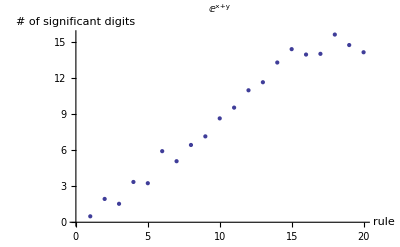

```mathematica
ClearAll[p,fun,a00,x,y,q,w]
p={{1,0},{0,2},{3,2}};
fun[{x_,y_}]:=Exp[x+y];
Print["Mathematica value = ",a00=NIntegrate[fun[{x,y}],{y,0,2},{x,1-y/2,1+y},WorkingPrecision->20]];
Table[
{q,w}=DunavantRule[rule,{{0,0},{1,0},{0,1}}];
-Log@Abs[(NIntegrateTriangleDunavantMethod[p,fun,{q,w}]-a00)/a00]/Log[10],
{rule,1,20}
]//ListPlot[#,AxesLabel->{"rule","# of significant digits"},AxesOrigin->{0,0},PlotLabel->fun[{x,y}]]&//Print;
```

Arcsinh method single triangle
	source triangle
	near-singular field point

Mathematica value=0.023963917173953-0.6902623825876617 ⅈ

best value=0.0239639-0.690262 ⅈ

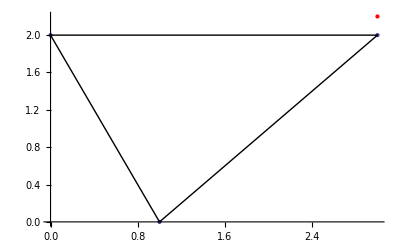

-Graphics3D-

```mathematica
ClearAll[P, P0,A, s1, s2, s3, wP, quadrules, iP]
P = {{1,0},{3,2},{0,2}} // N // ToPackedArray;
P0 = {3,2.2} // N // ToPackedArray;
A=Det[{P⟦2⟧-P⟦1⟧,P⟦3⟧-P⟦1⟧}];
s1 = A Det[{P[[1]] - P0, P[[2]] - P[[1]]}]>0;
s2 = A Det[{P[[2]] - P0, P[[3]] - P[[2]]}]>0;
s3 = A Det[{P[[3]] - P0, P[[1]] - P[[3]]}]>0;
wP = {1, 1, 1} // N // ToPackedArray;
If[!s1,wP⟦1⟧=-1.0];
If[!s2,wP⟦2⟧=-1.0];
If[!s3,wP⟦3⟧=-1.0];

ClearAll[fun, x, y, a0,a00]
fun[{x_, y_}] := Exp[ⅈ(x + 2y)];
raw = Table[
   quadrules = {LegendreRule[Nu, 0, 1], LegendreRule[Nv, 0, 1]};
   iP =
    {NIntegrateTriangleArcSinhMethod[{P0, P[[1]], P[[2]]}, fun, quadrules],
     NIntegrateTriangleArcSinhMethod[{P0, P[[2]], P[[3]]}, fun, quadrules],
     NIntegrateTriangleArcSinhMethod[{P0, P[[3]], P[[1]]}, fun, quadrules]};
   a1 = iP.wP;
   {Nu, Nv, a1}
   ,
   {Nu, 30}, {Nv, 10}];
a00=NIntegrate[fun[{x,y}]/Norm[{x,y}-P0],{y,0,2},{x,1-y/2,1+y},WorkingPrecision->16];
a0 = raw[[-1,-1, 3]];
Print["Mathematica value=",a00];
Print["best value=", a0];
data = {#[[1]], #[[2]], -Log@Abs[(#[[3]] - a0)/a0]/Log[10]} & /@ Flatten[raw, 1];
ListPlot[{P, {P0}}, PlotStyle -> {PointSize[Large], Red}, Epilog -> {Black, Line[P], Line[{P[[3]], P[[1]]}]}]
ListPlot3D[data, AxesLabel -> {"Nu", "Nv", "# of SD"}, PlotLabel -> fun[{x, y}],PlotRange->All,ImageSize -> Large]
```

Duffy - Only singular

In pt⟦np⟧: False

r={0.5,0.3}

cntr⟦np⟧={0.151174,0.758632}

|r-rp|≃0.576214

best value for m=0 is: 0.013379

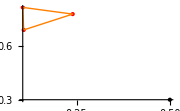
-Graphics-
-Graphics3D-

```mathematica
ClearAll[m,np,q,w,point,xx,data]
pStd={{0,0},{1,0},{0,1}};
m=0;
np=1;
point={0.5,0.3};
Print["In pt⟦np⟧: ",InTriangle[point,pt⟦np⟧]];
Print["r=",point];
Print["cntr⟦np⟧=",cntr⟦np⟧]
Print["|r-rp|≃",cntr⟦np⟧-point//Norm];
data=Table[{q,w}=QuadratureProduct2D[LegendreRule[n2,0,1],LegendreRule[n1,0,1]];
xx=0.0;
xx+=NIntegrateTriangleDuffyMethod[{point,pt⟦np,1⟧,pt⟦np,2⟧},VscnmFuncR[m,point,#]&,{q,w}];
xx+=NIntegrateTriangleDuffyMethod[{point,pt⟦np,2⟧,pt⟦np,3⟧},VscnmFuncR[m,point,#]&,{q,w}];
xx+=NIntegrateTriangleDuffyMethod[{point,pt⟦np,3⟧,pt⟦np,1⟧},VscnmFuncR[m,point,#]&,{q,w}];
{n1,n2,xx},{n1,30},{n2,30}]//Flatten[#,1]&;
Print["best value for m=",m," is: ",data⟦-1,3⟧];
Print@TableForm@{
ListPlot[{pt⟦np⟧,{point}},PlotStyle->{{Red,PointSize[Large]},{Black,PointSize[Large]}},Epilog->{Orange,Line[pt⟦np⟧],Line[{pt⟦np,1⟧,pt⟦np,3⟧}]},ImageSize->Small],
({#⟦1⟧,#⟦2⟧,-Log@Abs[#⟦3⟧-data⟦-1,3⟧]/Log[10]}&/@data)//ListPlot3D[#,PlotLabel->"DUFFY-SINGULAR "<>"m="<>ToString[m],AxesLabel->{"# of points","# of significant digits"},AxesOrigin->{0,0},ImageSize->Large]&};
```

Arcsinh method: Singular and near-singular and non-singular
Dunavant methods: Non-singular

In pt⟦np⟧: False

r={0.9,0.8}

cntr⟦np⟧={0.186399,0.306567}

|r-rp|≃0.867585

Rc = 0.0715497

best value for m= 40 is: 0.000176952+0.000298494 ⅈ

most # of SD by arcsinh = 6.46466 with 702 sampling points

most # of SD by Dunavant = 13.2249 with 79 sampling points

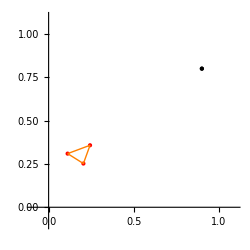
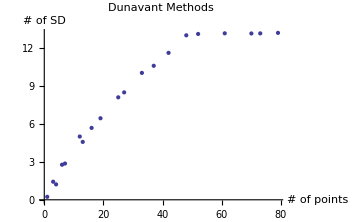
{-Graphics-,-Graphics3D-,-Graphics-}

```mathematica
ClearAll[m,np,point,a0,a1]
m=40;
np=23;
point={0.9,0.8};
Print["In pt⟦np⟧: ",InTriangle[point,pt⟦np⟧]];
Print["r=",point];
Print["cntr⟦np⟧=",cntr⟦np⟧]
Print["|r-rp|≃",cntr⟦np⟧-point//Norm];
Print["Rc = ",Rc⟦np⟧];
a0=NIntegrateTriangleArcSinh2[point,pt⟦np⟧,VscnmFuncR[m,point,#]&,{LegendreRule[100,0,1],LegendreRule[100,0,1]}];
raw1=Table[a1=NIntegrateTriangleArcSinh2[point,pt⟦np⟧,VscnmFuncR[m,point,#]&,{LegendreRule[Nu,0,1],LegendreRule[Nv,0,1]}];
{Nu,Nv,a1},{Nu,1.2m+30},{Nv,3}]//Flatten[#,1]&;
data1={#⟦1⟧,#⟦2⟧,-Log@Abs[(#⟦3⟧-a0)/a0]/Log[10]}&/@raw1;
raw2=Table[quadrules=DunavantRule[rule,{{0,0},{1,0},{0,1}}];{Length[quadrules⟦1⟧],NIntegrateTriangleDunavantMethod[pt⟦np⟧,VscnmFunc[m,point,#]&,quadrules]},{rule,1,20}];
data2={#⟦1⟧,-Log@Abs[(#⟦2⟧-a0)/a0]/Log[10]}&/@raw2;
Print["best value for m= ",m," is: ",a0];
Print["most # of SD by arcsinh = ",data1⟦-1,-1⟧," with ",3data1⟦-1,1⟧data1⟦-1,2⟧," sampling points"];
Print["most # of SD by Dunavant = ",data2⟦-1,-1⟧," with ",data2⟦-1,1⟧," sampling points"];
Print@{Show[
ListPlot[{pt⟦np⟧,{point}},PlotStyle->{{Red,PointSize[Large]},{Black,PointSize[Large]}},Epilog->{Orange,Line[pt⟦np⟧],Line[{pt⟦np,1⟧,pt⟦np,3⟧}]},ImageSize->250,PlotRange->{{-0.1,1.1},{-0.1,1.1}},AspectRatio->1]
],
ListPlot3D[data1,PlotRange->All,AxesLabel->{"Nu","Nv","# of SD"},PlotLabel->"ArcSinh Method",ImageSize->Medium],
ListPlot[data2,AxesLabel->{"# of points","# of SD"},PlotLabel->"Dunavant Methods",ImageSize->Medium]
}
```

Test the continuity of arcsinh method

```mathematica
ClearAll[quadrules,P,m,raw,xrange,yrange]
quadrules={LegendreRule[20,0,1],LegendreRule[4,0,1]};
P={{2,0},{3,2},{0,2}} // N // ToPackedArray;
m=0;
xrange=Range[0.001,3.0,0.03];
yrange=Range[-0.301,3.01,0.03];
raw=Table[{x,y,NIntegrateTriangleArcSinh2[{x,y},P,VscnmFuncR[m,{x,y},#]&,quadrules]},{y,yrange},{x,xrange}]//Flatten[#,1]&;
ListPlot3D[raw,InterpolationOrder->3,ImageSize->Large]
```

$Aborted

ListPlot3D::arrayerr: raw must be a valid array or a list of valid arrays.

ListPlot3D[raw,InterpolationOrder→3,ImageSize→Large]

12.3457

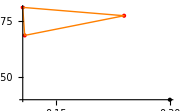

0.116115

```mathematica
ClearAll[n,m,ruleFar,ruleNear,mask,Mask,P,partialIntegral]
ruleFar=DunavantRule[5,{{-1,-1},{1,-1},{-1,1}}];
ruleNear={LegendreRule[8,0,1],LegendreRule[3,0,1]};
Mask[P_]:=Table[Norm[P-cntr⟦n⟧]>0.2,{n,Ns}]
{n,m}={1,0};
P={0.3,0.4};
mask=Mask[P];
Total[If[#,0,1]&/@mask]/Ns*100//N
Print@ListPlot[{pt⟦n⟧,{P}},PlotStyle->{{Red,PointSize[Large]},{Black,PointSize[Large]}},Epilog->{Orange,Line[pt⟦n⟧],Line[{pt⟦n,1⟧,pt⟦n,3⟧}]},ImageSize->Small]
partialIntegral=Table[
If[mask⟦n⟧,
(*Far Field*)
NIntegrateTriangleDunavantMethod[pt⟦n⟧,VscnmFunc[m,P,#]&,ruleFar]
,
(*Near Field*)
NIntegrateTriangleArcSinh2[P,pt⟦n⟧,VscnmFuncR[m,P,#]&,ruleNear]
]
,{n,Ns}];
partialIntegral//Total//Print
```

```mathematica
ClearAll[n,m,QUADRULES,raw,time]
{n,m}={10,0};
QUADRULES={
{DunavantRule[5,{{-1,-1},{1,-1},{-1,1}}],{LegendreRule[8,0,1],LegendreRule[3,0,1]}},
{DunavantRule[10,{{-1,-1},{1,-1},{-1,1}}],{LegendreRule[10,0,1],LegendreRule[3,0,1]}},
{DunavantRule[15,{{-1,-1},{1,-1},{-1,1}}],{LegendreRule[12,0,1],LegendreRule[3,0,1]}},
{DunavantRule[20,{{-1,-1},{1,-1},{-1,1}}],{LegendreRule[15,0,1],LegendreRule[3,0,1]}}
};
Print["time = ",time=(raw=Table[NField[cntr⟦n⟧,m,QUADRULES⟦i⟧]*area⟦n⟧,{i,Length[QUADRULES]},{m,0,Nd}];)//AbsoluteTiming//#⟦1⟧&];
```

$Aborted

Non-singular Bnmnpmp

dr=0.804774

Rc=0.0700684

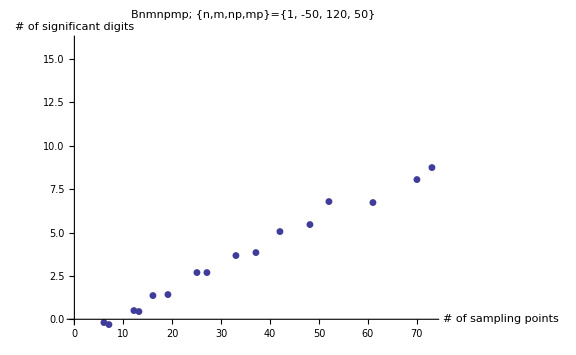

```mathematica
ClearAll[n,m,np,mp,ArcSinhFlag,quadrules]
{n,m}={1,-50};
{np,mp}={120,50};
Print["dr=",Norm[cntr⟦n⟧-cntr⟦np⟧]];
Print["Rc=",Rc//Mean];
ArcSinhFlag=False;
raw=Table[
quadrules=DunavantRule[rule,{{0,0},{1,0},{0,1}}];
{quadrules⟦1⟧//Length,Bnmnpmp[n,m,np,mp,ArcSinhFlag,quadrules]},
{rule,20}
];
a0=raw⟦-1,2⟧;
data={#⟦1⟧,-Log@Abs[(#⟦2⟧-a0)/a0]/Log[10]}&/@raw;
ListPlot[data,PlotRange->{0,16},AxesLabel->{"# of sampling points","# of significant digits"},PlotLabel->"Bnmnpmp; {n,m,np,mp}="<>ToString[{n,m,np,mp}],ImageSize->Large,PlotMarkers->Automatic]
```

Singular Bnmnpmp

```mathematica
ClearAll[n,m,np,mp,ArcSinhFlag,quadrules]
{n,m}={1,10};
{np,mp}={1,0};
Print["dr=",Norm[cntr⟦n⟧-cntr⟦np⟧]];
Print["Rc=",Rc//Mean];
ArcSinhFlag=True;
raw=Table[
quadrules={LegendreRule[Nu,0,1],LegendreRule[Nv,0,1]};
{Nu,Nv,Bnmnpmp[n,m,np,mp,ArcSinhFlag,quadrules]},
{Nu,100},{Nv,3}
]//Flatten[#,1]&;
a0=raw⟦-1,3⟧;
data={#⟦1⟧,#⟦2⟧,-Log@Abs[(#⟦3⟧-a0)/a0]/Log[10]}&/@raw;
ListPlot3D[data,PlotRange->{0,16},AxesLabel->{"# of sampling points","# of significant digits"},PlotLabel->"Bnmnpmp; {n,m,np,mp}="<>ToString[{n,m,np,mp}],ImageSize->Large]
```

dr=0.

Rc=0.0700684

-Graphics3D-

Non-singular SVD

dr=0.728111

Rc=0.0700684

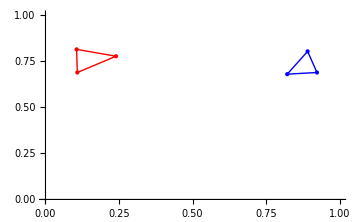

Dim/@{u,w,v}={{81,10},{10,10},{81,10}}

Max relative diff = 7.44206×10^-14

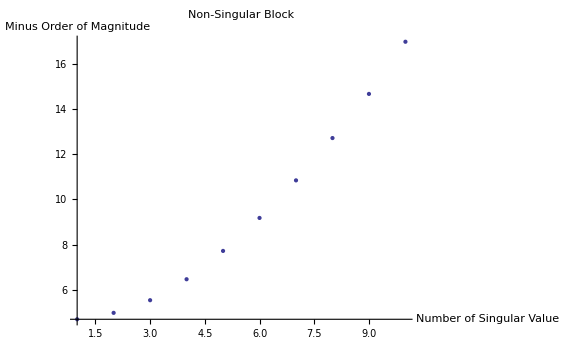

```mathematica
ClearAll[n,np,ArcSinhFlag,quadrules,raw]
{n,np}={1,10};
Print["dr=",Norm[cntr⟦n⟧-cntr⟦np⟧]];
Print["Rc=",Rc//Mean];
Show[
ListPlot[pt⟦n⟧,ImageSize->Medium,PlotStyle->{Red,PointSize[Large]},PlotRange->{{0,1},{0,1}},Epilog->{Red,Line[pt⟦n⟧],Line[{pt⟦n,3⟧,pt⟦n,1⟧}],Blue,Line[pt⟦np⟧],Line[{pt⟦np,3⟧,pt⟦np,1⟧}]}],
ListPlot[pt⟦np⟧,PlotStyle->{Blue,PointSize[Medium]}]
]
ArcSinhFlag=False;
quadrules=DunavantRule[12,{{0,0},{1,0},{0,1}}];
raw=ParallelTable[Bnmnpmp[n,m,np,mp,ArcSinhFlag,quadrules],{m,-Nd,Nd},{mp,-Nd,Nd}];
-Log@Abs[SingularValueList[raw]]/Log[10]//ListPlot;
ClearAll[rank,u,w,v]
rank=Length[SingularValueList[raw]];
{u,w,v}=SingularValueDecomposition[raw,rank];
Print["Dim/@{u,w,v}=",Dimensions/@{u,w,v}];
Print["Max relative diff = ",Norm/@Flatten[(u.w.v†-raw)/raw]//Max];
-Log@Abs[SingularValueList[raw]]/Log[10]//ListPlot[#,PlotRange->All,AxesLabel->{"Number of Singular Value","Minus Order of Magnitude"},PlotLabel->"Non-Singular Block",ImageSize->Large]&
```

Singular block analysis - banded structure

dr=0.

Rc=0.0700684

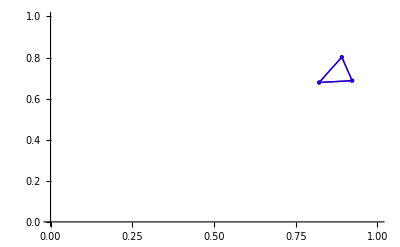

```mathematica
ClearAll[Nu,Nv,n,np,ArcSinhFlag,quadrules,raw]
{Nu,Nv}={100,3};
{n,np}={10,10};
Print["dr=",Norm[cntr⟦n⟧-cntr⟦np⟧]];
Print["Rc=",Rc//Mean];
Show[
ListPlot[pt⟦n⟧,PlotStyle->{Red,PointSize[Large]},PlotRange->{{0,1},{0,1}},Epilog->{Red,Line[pt⟦n⟧],Line[{pt⟦n,3⟧,pt⟦n,1⟧}],Blue,Line[pt⟦np⟧],Line[{pt⟦np,3⟧,pt⟦np,1⟧}]}],
ListPlot[pt⟦np⟧,PlotStyle->{Blue,PointSize[Medium]}]
]
ArcSinhFlag=True;
quadrules={LegendreRule[Nu,0,1],LegendreRule[Nv,0,1]};
raw=ParallelTable[Bnmnpmp[n,m,np,mp,ArcSinhFlag,quadrules],{m,-Nd,Nd},{mp,-Nd,Nd}];
```

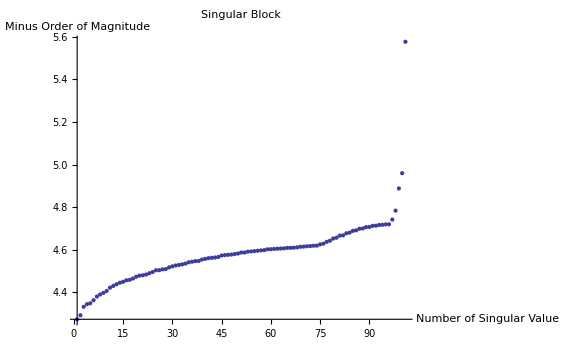

```mathematica
-Log@Abs[SingularValueList[raw]]/Log[10]//ListPlot[#,PlotRange->All,AxesLabel->{"Number of Singular Value","Minus Order of Magnitude"},PlotLabel->"Singular Block",ImageSize->Large]&
```

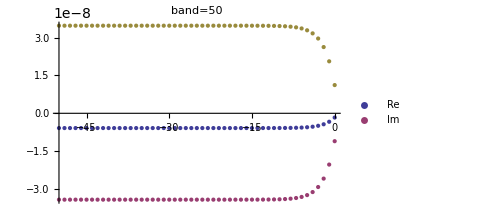
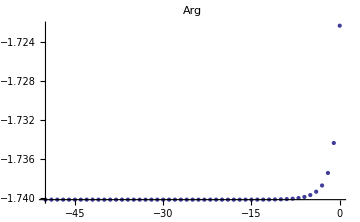

```mathematica
ClearAll[diagRe,diagIm,diagNorm,diagArg,band]
band=50;
diagRe=Table[{i-Nd-1,raw⟦i+band,i⟧//Re},{i,1,Nm-band}];
diagIm=Table[{i-Nd-1,raw⟦i+band,i⟧//Im},{i,1,Nm-band}];
diagNorm=Table[{i-Nd-1,raw⟦i+band,i⟧//Norm},{i,1,Nm-band}];
diagArg=Table[{i-Nd-1,raw⟦i+band,i⟧//Arg},{i,1,Nm-band}];
{
ListPlot[{diagRe,diagIm,diagNorm},PlotRange->All,PlotStyle->{{},{Thick,Dashed}},PlotLabel->"band="<>ToString[band],PlotLegends->{"Re","Im"},ImageSize->Medium],
diagArg//ListPlot[#,PlotRange->All,PlotLabel->"Arg",ImageSize->Medium]&
}
```

FittedModel[-5.85312×10^-9+6.94121×10^-9 ⅇ^(-0.510826 x)]

FittedModel[-5.85312×10^-9+6.94121×10^-9 ⅇ^(-0.510826 x)]

Max relative err=1.82842×10^-10

Max relative err=1.24223×10^-13

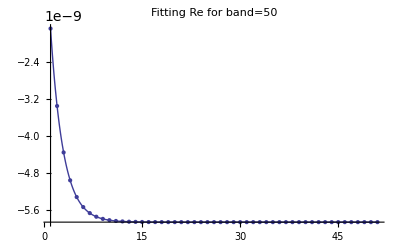

FittedModel[3.42237×10^-8-3.86154×10^-8 ⅇ^(-0.510826 x)]

FittedModel[-106.52+106.52 ⅇ^(-1. x)]

Max relative err=1.55386×10^-10

Max relative err=-3.11245×10^9

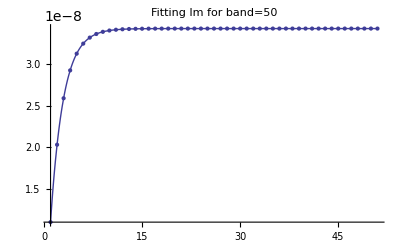

```mathematica
ClearAll[band,rawp,range,lm1,lm1p,lm2,lm2p,a,b,c,x]
range={1,2,3,4,Nd+1};
band=Nd;
rawp=Table[raw⟦i,i+band⟧//Re,{i,1,Nm-band}];
(lm1=NonlinearModelFit[rawp,a+c Exp[-b x],{a,b,c},x])//Print
(lm1p=NonlinearModelFit[Table[{i,raw⟦i,i+band⟧}//Re,{i,range}],a+c Exp[-b x],{a,b,c},x])//Print
Max[Table[(lm1[i]-rawp⟦i⟧)/rawp⟦i⟧,{i,1,Nm-band}]]//Print["Max relative err=",#]&
Max[Table[(lm1p[i]-rawp⟦i⟧)/rawp⟦i⟧,{i,1,Nm-band}]]//Print["Max relative err=",#]&
Show[
ListPlot[rawp,PlotRange->All,PlotLabel->"Fitting Re for band=50"],
Plot[lm1p[x],{x,1,Nd+1},PlotRange->All]
]//Print
rawp=Table[raw⟦i,i+band⟧//Im,{i,1,Nm-band}];
(lm2=NonlinearModelFit[rawp,-a-c Exp[-b x],{a,b,c},x])//Print
(lm2p=NonlinearModelFit[Table[{i,raw⟦i,i+band⟧}//Im,{i,range}],a+c Exp[-b x],{a,b,c},x])//Print
Max[Table[(lm2[i]-rawp⟦i⟧)/rawp⟦i⟧,{i,1,Nm-band}]]//Print["Max relative err=",#]&
Max[Table[(lm2p[i]-rawp⟦i⟧)/rawp⟦i⟧,{i,1,Nm-band}]]//Print["Max relative err=",#]&
Show[
ListPlot[rawp,PlotRange->All,PlotLabel->"Fitting Im for band=50"],
Plot[lm2[x],{x,1,Nd+1},PlotRange->All]
]//Print
```

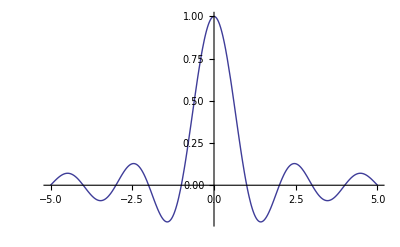

```mathematica
Plot[Sinc[π x],{x,-5,5},PlotRange->All]
```

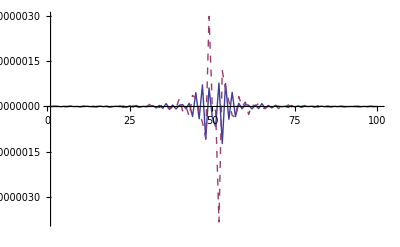

```mathematica
ClearAll[Δm,rawp2]
rawp2=Table[raw⟦i,Nm-i⟧,{i,1,Nm}];
ListLinePlot[{Re[rawp2],Im[rawp2]},PlotStyle->{{},{Dashed,Thick}},PlotRange->All]
```

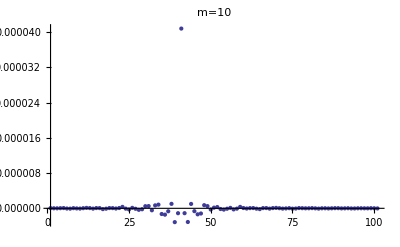

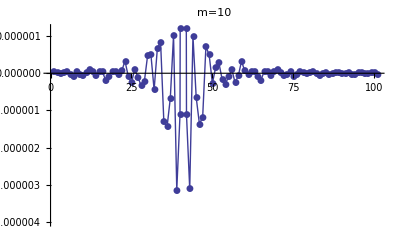

```mathematica
ClearAll[m]
m=10;
ListPlot[Re@raw⟦Nd+1-m⟧,PlotRange->All,PlotLabel->"m="<>ToString[m]]
ListLinePlot[Re@raw⟦Nd+1-m⟧,PlotRange->{-0.000004,0.0000012},PlotMarkers->Automatic,PlotLabel->"m="<>ToString[m]]
```

Cross approximation on non-singular blocks

```mathematica
ClearAll[MaxValueLocationC]
MaxValueLocationC=Compile[{{a,_Complex,2}},
Module[{i,j,i0,j0,m,n,max},{m,n}=Dimensions[a];{i0,j0}={1,1};max=Abs[a⟦1,1⟧];
For[i=1,i≤m,i++,For[j=1,j≤n,j++,If[Abs[a⟦i,j⟧]>max,{i0,j0}={i,j};max=Abs[a⟦i0,j0⟧];];];];
{i0,j0}]];
```

dr=0.804774

Rc=0.0700684

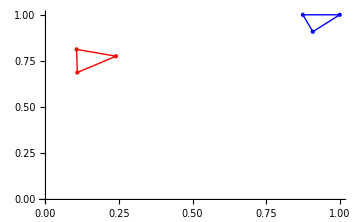

```mathematica
ClearAll[n, np, ArcSinhFlag, quadrules, raw]
{n, np} = {1, 120};
Print["dr=", Norm[cntr[[n]] - cntr[[np]]]];
Print["Rc=", Rc // Mean];
Show[
  ListPlot[pt[[n]], ImageSize -> Medium, PlotStyle -> {Red, PointSize[Large]}, PlotRange -> {{0, 1}, {0, 1}}, Epilog -> {Red, Line[pt[[n]]], Line[{pt[[n, 3]], pt[[n, 1]]}], Blue, Line[pt[[np]]], Line[{pt[[np, 3]], pt[[np, 1]]}]}],
  ListPlot[pt[[np]], PlotStyle -> {Blue, PointSize[Medium]}]
  ] // Print
ArcSinhFlag = False;
quadrules = DunavantRule[20, {{0, 0}, {1, 0}, {0, 1}}];
raw = ParallelTable[Bnmnpmp[n, m, np, mp, ArcSinhFlag, quadrules], {m, -Nd, Nd}, {mp, -Nd, Nd}];
```

FittedModel[-3.3018×10^-7+2.07802×10^-7 ⅇ^(-0.510826 x)]

3.81764×10^-11

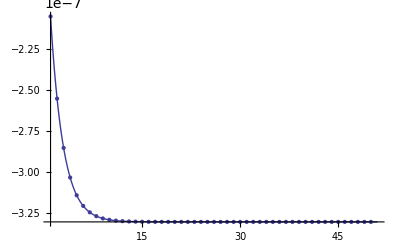

```mathematica
ClearAll[diagRe,band,a,b,c,x];
band=Nd+1;
diagRe=Table[raw⟦i,i+band⟧//Re,{i,1,Nm-band}];
(lm=NonlinearModelFit[Table[{i,raw⟦i,i+band⟧//Re},{i,1,Nm-band}],a+b Exp[-c x],{a,b,c},x])//Print
Max[Table[Norm[(lm[i]-raw⟦i,i+band⟧//Re)/(raw⟦i,i+band⟧//Re)],{i,1,Nm-band}]]//Print
Show[
ListPlot[diagRe,PlotRange->All],
Plot[lm[x],{x,1,Nd+1},PlotRange->All]
]
```

Check accuracy: Norm[Z-∑_ν a bᵀ]/Norm[Z]=3.4095×10^-15

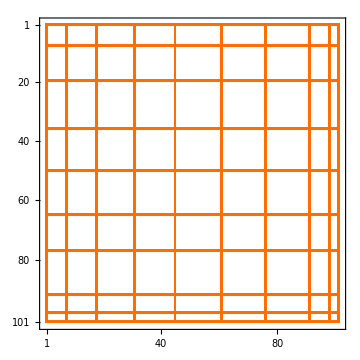

```mathematica
ClearAll[ν,i0,j0,A,B,R]
eps=1.0*10^-14;
R=raw;
A={};
B={};
ROW={};
COL={};
For[ν=1,ν≤10,ν++,
{i0,j0}=MaxValueLocationC[R];
If[(xx=Abs[R⟦i0,j0⟧]/Norm[raw,"Frobenius"])<eps,
Print["Terminate: rank=",ν-1,", eps=",xx];Break[];
];
AppendTo[ROW,i0];
AppendTo[COL,j0];
AppendTo[A,R⟦All,j0⟧];
AppendTo[B,R⟦i0⟧/R⟦i0,j0⟧];
R=R-Outer[Times,A⟦ν⟧,B⟦ν⟧];
];
Print["Check accuracy: Norm[Z-∑_ν a bᵀ]/Norm[Z]=",
Norm[raw-∑_(ν=1)^Length[A] Outer[Times,A⟦ν⟧,B⟦ν⟧]]/Norm[raw]];

ClearAll[PrintO]
PrintO[Nm_,row_,col_]:=Module[{n,r,A},
r=Length[row];A=ConstantArray[0,{Nm,Nm}];
For[n=1,n≤r,n++,
A⟦All,col⟦n⟧⟧=1;
A⟦row⟦n⟧,All⟧=1;
];
MatrixPlot[A]
]
PrintO[Nm,ROW,COL]//Print
```

```mathematica
ROW
COL
```

{1,61,31,48,12,56,5,22}

{1,61,26,46,10,55,17,37}

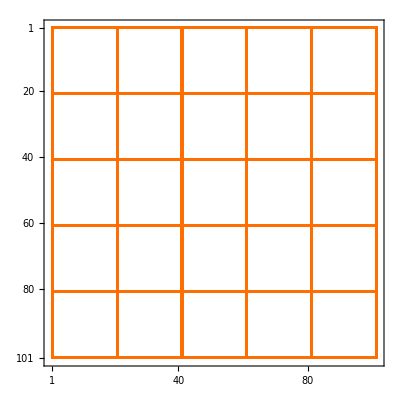

```mathematica
ROW=Range[1,Nm,20];
COL=ROW;
PrintO[Nm,ROW,COL]//Print
```

```mathematica
ClearAll[U,VT,S,eps,u,w,v]
U=raw⟦All,COL⟧;
VT=raw⟦ROW⟧;
S=Outer[raw⟦#1,#2⟧&,ROW,COL];
eps=10^-10;
{u,w,v}=SingularValueDecomposition[S,Length@SingularValueList[S,Tolerance->eps]];
Norm/@((S-u.w.vᵀ*)/S)//Max
Norm/@((U.(v.Inverse[w].uᵀ*).VT-raw)/raw)//Max
Length[w]
```

3.00512×10^-10

2.69937×10^-7

8

### Toeplitz Compression

DunavantMethod uses quadrature rules generated by
	DunavantRule[rule,{{0,0},{0,1},{1,0}}]
where
	rule is an integer between 1 and 20

ArcSinhMethod uses quadrature rules
	{LegendreRule[Nu,0,1],
	LegendreRule[Nv,0,1]}
where
	Nu and Nv are the number of sampling points in the u- and the v- directions

```mathematica
ClearAll[BtBandFunc,BtBandFuncR,BsBandFunc,BsBandFuncR,BtBandArcSinhMethod,BtBandDunavantMethod,BsBandArcSinhMethod,BsBandDunavantMethod]
BtBandFunc[Δm_,r_,rp_]:=Module[{dr,phir2rp},dr=r-rp;
If[Norm[dr]<1.0*10^-13,phir2rp=0.0,phir2rp=ArcTan[dr⟦1⟧,dr⟦2⟧]];
mut[rp]Exp[-ⅈ Δm phir2rp]/Norm[dr]
]
BtBandFuncR[Δm_,r_,rp_]:=Module[{dr,phir2rp},dr=r-rp;
If[Norm[dr]<1.0*10^-13,phir2rp=0.0,phir2rp=ArcTan[dr⟦1⟧,dr⟦2⟧]];
mut[rp]Exp[-ⅈ Δm phir2rp]
]
BsBandFunc[Δm_,r_,rp_]:=Module[{dr,phir2rp},dr=r-rp;
If[Norm[dr]<1.0*10^-13,phir2rp=0.0,phir2rp=ArcTan[dr⟦1⟧,dr⟦2⟧]];
-mus[rp]Exp[-ⅈ Δm phir2rp]/Norm[dr]
]
BsBandFuncR[Δm_,r_,rp_]:=Module[{dr,phir2rp},dr=r-rp;
If[Norm[dr]<1.0*10^-13,phir2rp=0.0,phir2rp=ArcTan[dr⟦1⟧,dr⟦2⟧]];
-mus[rp]Exp[-ⅈ Δm phir2rp]
]

BtBandDunavantMethod[n_,np_,Δm_,quadrules_]:=area⟦n⟧area⟦np⟧*
NIntegrateTriangleDunavantMethod[pt⟦np⟧,BtBandFunc[Δm,cntr⟦n⟧,#]&,quadrules]
BtBandArcSinhMethod[n_,np_,Δm_,quadrules_]:=area⟦n⟧area⟦np⟧*
NIntegrateTriangleArcSinh2[cntr⟦n⟧,pt⟦np⟧,BtBandFuncR[Δm,cntr⟦n⟧,#]&,quadrules]
BsBandDunavantMethod[n_,np_,Δm_,quadrules_]:=area⟦n⟧area⟦np⟧*
NIntegrateTriangleDunavantMethod[pt⟦np⟧,BsBandFunc[Δm,cntr⟦n⟧,#]&,quadrules]
BsBandArcSinhMethod[n_,np_,Δm_,quadrules_]:=area⟦n⟧area⟦np⟧*
NIntegrateTriangleArcSinh2[cntr⟦n⟧,pt⟦np⟧,BsBandFuncR[Δm,cntr⟦n⟧,#]&,quadrules]
```

Test elementwise correctness of the new matrix elements

```mathematica
ClearAll[n,m,np,mp,quadrules]
{n,m,np,mp}={1,14,120,30};
quadrules=DunavantRule[20,{{0,0},{1,0},{0,1}}];
raw=Bnmnpmp[n,m,np,mp,False,quadrules]
BtBandDunavantMethod[n,np,m-mp,quadrules]+BsBandDunavantMethod[n,np,m-mp,quadrules]gTbl⟦mp+Nd+1⟧
```

Part::partd: Part specification pt ⟦ 120 ⟧ is longer than depth of object.

Part::partw: Part 3 of pt ⟦ 120 ⟧ does not exist.

Transpose::nmtx: The first two levels of the one-dimensional list {120 - pt, -pt + pt ⟦ 120 ⟧ ⟦ 3 ⟧} cannot be transposed.

Part::partd: Part specification cntr ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

0.5 Abs[Det[Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}]]] area⟦1⟧ area⟦120⟧ ((0.000704405 ⅇ^(16 ⅈ phir2rp$10307) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00836815,0.146965}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00836815,0.146965}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00836815,0.146965}+cntr⟦1⟧]+(0.000704405 ⅇ^(16 ⅈ phir2rp$10312) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00836815,0.861403}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00836815,0.861403}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00836815,0.861403}+cntr⟦1⟧]+(0.000867019 ⅇ^(16 ⅈ phir2rp$10247) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00190093,0.50095}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00190093,0.50095}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00190093,0.50095}+cntr⟦1⟧]+(0.00483903 ⅇ^(16 ⅈ phir2rp$10283) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.00631412,0.377843}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.00631412,0.377843}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.00631412,0.377843}+cntr⟦1⟧]+(0.00483903 ⅇ^(16 ⅈ phir2rp$10288) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.00631412,0.615843}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.00631412,0.615843}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.00631412,0.615843}+cntr⟦1⟧]+(0.00357391 ⅇ^(16 ⅈ phir2rp$10319) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0105477,0.0596961}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0105477,0.0596961}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0105477,0.0596961}+cntr⟦1⟧]+(0.00357391 ⅇ^(16 ⅈ phir2rp$10324) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0105477,0.929756}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0105477,0.929756}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0105477,0.929756}+cntr⟦1⟧]+(0.00175113 ⅇ^(16 ⅈ phir2rp$10275) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0115819,0.0115819}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0115819,0.0115819}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0115819,0.0115819}+cntr⟦1⟧]+(0.00175113 ⅇ^(16 ⅈ phir2rp$10276) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0115819,0.976836}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0115819,0.976836}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0115819,0.976836}+cntr⟦1⟧]+(0.00847109 ⅇ^(16 ⅈ phir2rp$10295) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0139739,0.249419}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0139739,0.249419}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0139739,0.249419}+cntr⟦1⟧]+(0.00847109 ⅇ^(16 ⅈ phir2rp$10300) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0139739,0.736607}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0139739,0.736607}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0139739,0.736607}+cntr⟦1⟧]+(0.0116601 ⅇ^(16 ⅈ phir2rp$10250) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0235741,0.488213}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0235741,0.488213}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0235741,0.488213}+cntr⟦1⟧]+(0.0101127 ⅇ^(16 ⅈ phir2rp$10313) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0266861,0.137727}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0266861,0.137727}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0266861,0.137727}+cntr⟦1⟧]+(0.0101127 ⅇ^(16 ⅈ phir2rp$10318) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0266861,0.835587}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0266861,0.835587}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0266861,0.835587}+cntr⟦1⟧]-(0.00063206 ⅇ^(16 ⅈ phir2rp$10272) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0416187,0.0416187}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0416187,0.0416187}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0416187,0.0416187}+cntr⟦1⟧]-(0.00063206 ⅇ^(16 ⅈ phir2rp$10273) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0416187,0.916763}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0416187,0.916763}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0416187,0.916763}+cntr⟦1⟧]+(0.0164658 ⅇ^(16 ⅈ phir2rp$10277) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0487416,0.344856}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0487416,0.344856}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0487416,0.344856}+cntr⟦1⟧]+(0.0164658 ⅇ^(16 ⅈ phir2rp$10282) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0487416,0.606403}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0487416,0.606403}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0487416,0.606403}+cntr⟦1⟧]+(0.0076983 ⅇ^(16 ⅈ phir2rp$10269) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.053069,0.053069}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.053069,0.053069}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.053069,0.053069}+cntr⟦1⟧]+(0.0076983 ⅇ^(16 ⅈ phir2rp$10270) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.053069,0.893862}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.053069,0.893862}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.053069,0.893862}+cntr⟦1⟧]+(0.00357391 ⅇ^(16 ⅈ phir2rp$10322) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0596961,0.0105477}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0596961,0.0105477}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0596961,0.0105477}+cntr⟦1⟧]+(0.00357391 ⅇ^(16 ⅈ phir2rp$10320) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0596961,0.929756}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0596961,0.929756}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0596961,0.929756}+cntr⟦1⟧]+(0.0183549 ⅇ^(16 ⅈ phir2rp$10301) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0755491,0.212776}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0755491,0.212776}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0755491,0.212776}+cntr⟦1⟧]+(0.0183549 ⅇ^(16 ⅈ phir2rp$10306) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0755491,0.711675}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0755491,0.711675}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0755491,0.711675}+cntr⟦1⟧]+(0.0228769 ⅇ^(16 ⅈ phir2rp$10253) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0897266,0.455137}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0897266,0.455137}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.0897266,0.455137}+cntr⟦1⟧]+(0.0159974 ⅇ^(16 ⅈ phir2rp$10266) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.104171,0.104171}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.104171,0.104171}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.104171,0.104171}+cntr⟦1⟧]+(0.0159974 ⅇ^(16 ⅈ phir2rp$10267) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.104171,0.791658}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.104171,0.791658}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.104171,0.791658}+cntr⟦1⟧]+(0.0258049 ⅇ^(16 ⅈ phir2rp$10289) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.134317,0.306635}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.134317,0.306635}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.134317,0.306635}+cntr⟦1⟧]+(0.0258049 ⅇ^(16 ⅈ phir2rp$10294) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.134317,0.559048}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.134317,0.559048}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.134317,0.559048}+cntr⟦1⟧]+(0.0101127 ⅇ^(16 ⅈ phir2rp$10316) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.137727,0.0266861}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.137727,0.0266861}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.137727,0.0266861}+cntr⟦1⟧]+(0.0101127 ⅇ^(16 ⅈ phir2rp$10314) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.137727,0.835587}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.137727,0.835587}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.137727,0.835587}+cntr⟦1⟧]+(0.000704405 ⅇ^(16 ⅈ phir2rp$10310) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.146965,-0.00836815}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.146965,-0.00836815}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.146965,-0.00836815}+cntr⟦1⟧]+(0.000704405 ⅇ^(16 ⅈ phir2rp$10308) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.146965,0.861403}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.146965,0.861403}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.146965,0.861403}+cntr⟦1⟧]+(0.0243681 ⅇ^(16 ⅈ phir2rp$10263) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.176488,0.176488}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.176488,0.176488}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.176488,0.176488}+cntr⟦1⟧]+(0.0243681 ⅇ^(16 ⅈ phir2rp$10264) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.176488,0.647023}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.176488,0.647023}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.176488,0.647023}+cntr⟦1⟧]+(0.030449 ⅇ^(16 ⅈ phir2rp$10256) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.196007,0.401996}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.196007,0.401996}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.196007,0.401996}+cntr⟦1⟧]+(0.0183549 ⅇ^(16 ⅈ phir2rp$10304) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.212776,0.0755491}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.212776,0.0755491}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.212776,0.0755491}+cntr⟦1⟧]+(0.0183549 ⅇ^(16 ⅈ phir2rp$10302) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.212776,0.711675}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.212776,0.711675}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.212776,0.711675}+cntr⟦1⟧]+(0.00847109 ⅇ^(16 ⅈ phir2rp$10298) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.249419,0.0139739}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.249419,0.0139739}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.249419,0.0139739}+cntr⟦1⟧]+(0.00847109 ⅇ^(16 ⅈ phir2rp$10296) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.249419,0.736607}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.249419,0.736607}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.249419,0.736607}+cntr⟦1⟧]+(0.0306249 ⅇ^(16 ⅈ phir2rp$10260) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.255893,0.255893}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.255893,0.255893}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.255893,0.255893}+cntr⟦1⟧]+(0.0306249 ⅇ^(16 ⅈ phir2rp$10261) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.255893,0.488214}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.255893,0.488214}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.255893,0.488214}+cntr⟦1⟧]+(0.0258049 ⅇ^(16 ⅈ phir2rp$10292) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.306635,0.134317}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.306635,0.134317}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.306635,0.134317}+cntr⟦1⟧]+(0.0258049 ⅇ^(16 ⅈ phir2rp$10290) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.306635,0.559048}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.306635,0.559048}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.306635,0.559048}+cntr⟦1⟧]+(0.0330571 ⅇ^(16 ⅈ phir2rp$10246) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.333333,0.333333}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.333333,0.333333}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.333333,0.333333}+cntr⟦1⟧]+(0.0164658 ⅇ^(16 ⅈ phir2rp$10280) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.344856,0.0487416}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.344856,0.0487416}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.344856,0.0487416}+cntr⟦1⟧]+(0.0164658 ⅇ^(16 ⅈ phir2rp$10278) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.344856,0.606403}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.344856,0.606403}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.344856,0.606403}+cntr⟦1⟧]+(0.00483903 ⅇ^(16 ⅈ phir2rp$10286) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.377843,0.00631412}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.377843,0.00631412}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.377843,0.00631412}+cntr⟦1⟧]+(0.00483903 ⅇ^(16 ⅈ phir2rp$10284) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.377843,0.615843}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.377843,0.615843}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.377843,0.615843}+cntr⟦1⟧]+(0.030449 ⅇ^(16 ⅈ phir2rp$10258) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.401996,0.196007}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.401996,0.196007}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.401996,0.196007}+cntr⟦1⟧]+(0.030449 ⅇ^(16 ⅈ phir2rp$10257) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.401996,0.401996}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.401996,0.401996}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.401996,0.401996}+cntr⟦1⟧]+(0.0228769 ⅇ^(16 ⅈ phir2rp$10255) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.455137,0.0897266}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.455137,0.0897266}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.455137,0.0897266}+cntr⟦1⟧]+(0.0228769 ⅇ^(16 ⅈ phir2rp$10254) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.455137,0.455137}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.455137,0.455137}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.455137,0.455137}+cntr⟦1⟧]+(0.0116601 ⅇ^(16 ⅈ phir2rp$10252) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.488213,0.0235741}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.488213,0.0235741}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.488213,0.0235741}+cntr⟦1⟧]+(0.0116601 ⅇ^(16 ⅈ phir2rp$10251) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.488213,0.488213}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.488213,0.488213}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.488213,0.488213}+cntr⟦1⟧]+(0.0306249 ⅇ^(16 ⅈ phir2rp$10259) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.488214,0.255893}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.488214,0.255893}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.488214,0.255893}+cntr⟦1⟧]+(0.000867019 ⅇ^(16 ⅈ phir2rp$10249) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.50095,-0.00190093}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.50095,-0.00190093}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.50095,-0.00190093}+cntr⟦1⟧]+(0.000867019 ⅇ^(16 ⅈ phir2rp$10248) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.50095,0.50095}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.50095,0.50095}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.50095,0.50095}+cntr⟦1⟧]+(0.0258049 ⅇ^(16 ⅈ phir2rp$10291) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.559048,0.134317}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.559048,0.134317}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.559048,0.134317}+cntr⟦1⟧]+(0.0258049 ⅇ^(16 ⅈ phir2rp$10293) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.559048,0.306635}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.559048,0.306635}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.559048,0.306635}+cntr⟦1⟧]+(0.0164658 ⅇ^(16 ⅈ phir2rp$10279) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.606403,0.0487416}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.606403,0.0487416}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.606403,0.0487416}+cntr⟦1⟧]+(0.0164658 ⅇ^(16 ⅈ phir2rp$10281) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.606403,0.344856}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.606403,0.344856}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.606403,0.344856}+cntr⟦1⟧]+(0.00483903 ⅇ^(16 ⅈ phir2rp$10285) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.615843,0.00631412}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.615843,0.00631412}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.615843,0.00631412}+cntr⟦1⟧]+(0.00483903 ⅇ^(16 ⅈ phir2rp$10287) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.615843,0.377843}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.615843,0.377843}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.615843,0.377843}+cntr⟦1⟧]+(0.0243681 ⅇ^(16 ⅈ phir2rp$10262) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.647023,0.176488}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.647023,0.176488}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.647023,0.176488}+cntr⟦1⟧]+(0.0183549 ⅇ^(16 ⅈ phir2rp$10303) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.711675,0.0755491}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.711675,0.0755491}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.711675,0.0755491}+cntr⟦1⟧]+(0.0183549 ⅇ^(16 ⅈ phir2rp$10305) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.711675,0.212776}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.711675,0.212776}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.711675,0.212776}+cntr⟦1⟧]+(0.00847109 ⅇ^(16 ⅈ phir2rp$10297) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.736607,0.0139739}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.736607,0.0139739}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.736607,0.0139739}+cntr⟦1⟧]+(0.00847109 ⅇ^(16 ⅈ phir2rp$10299) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.736607,0.249419}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.736607,0.249419}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.736607,0.249419}+cntr⟦1⟧]+(0.0159974 ⅇ^(16 ⅈ phir2rp$10265) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.791658,0.104171}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.791658,0.104171}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.791658,0.104171}+cntr⟦1⟧]+(0.0101127 ⅇ^(16 ⅈ phir2rp$10315) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.835587,0.0266861}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.835587,0.0266861}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.835587,0.0266861}+cntr⟦1⟧]+(0.0101127 ⅇ^(16 ⅈ phir2rp$10317) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.835587,0.137727}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.835587,0.137727}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.835587,0.137727}+cntr⟦1⟧]+(0.000704405 ⅇ^(16 ⅈ phir2rp$10309) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.861403,-0.00836815}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.861403,-0.00836815}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.861403,-0.00836815}+cntr⟦1⟧]+(0.000704405 ⅇ^(16 ⅈ phir2rp$10311) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.861403,0.146965}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.861403,0.146965}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.861403,0.146965}+cntr⟦1⟧]+(0.0076983 ⅇ^(16 ⅈ phir2rp$10268) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.893862,0.053069}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.893862,0.053069}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.893862,0.053069}+cntr⟦1⟧]-(0.00063206 ⅇ^(16 ⅈ phir2rp$10271) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.916763,0.0416187}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.916763,0.0416187}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.916763,0.0416187}+cntr⟦1⟧]+(0.00357391 ⅇ^(16 ⅈ phir2rp$10321) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.929756,0.0105477}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.929756,0.0105477}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.929756,0.0105477}+cntr⟦1⟧]+(0.00357391 ⅇ^(16 ⅈ phir2rp$10323) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.929756,0.0596961}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.929756,0.0596961}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.929756,0.0596961}+cntr⟦1⟧]+(0.00175113 ⅇ^(16 ⅈ phir2rp$10274) (mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.976836,0.0115819}]-mus[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.976836,0.0115819}] Phasef[30]))/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{0.976836,0.0115819}+cntr⟦1⟧])

Part::partd: Part specification area ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification area ⟦ 120 ⟧ is longer than depth of object.

Part::partd: Part specification pt ⟦ 120 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 3 of pt ⟦ 120 ⟧ does not exist.

Transpose::nmtx: The first two levels of the one-dimensional list {120 - pt, -pt + pt ⟦ 120 ⟧ ⟦ 3 ⟧} cannot be transposed.

Part::partw: Part 3 of pt ⟦ 120 ⟧ does not exist.

Transpose::nmtx: The first two levels of the one-dimensional list {120 - pt, -pt + pt ⟦ 120 ⟧ ⟦ 3 ⟧} cannot be transposed.

Part::pspec: Part specification 31 + Nd is neither a machine-sized integer nor a list of machine-sized integers.

0.5 Abs[Det[Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}]]] ((0.000704405 ⅇ^(«1») mut[pt+Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00836815,0.146965}])/Norm[-pt-Transpose[{120-pt,-pt+pt⟦120⟧⟦3⟧}].{-0.00836815,0.146965}+cntr⟦1⟧]+«80»+(«1»)/Norm[-pt-«1»+cntr⟦1⟧]) area⟦1⟧ area⟦120⟧+0.5 «4» gTbl⟦31+Nd⟧

Test the FFT - prepare

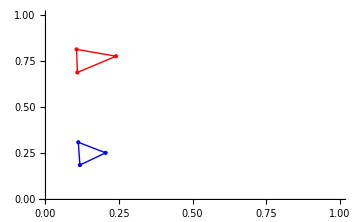

```mathematica
ClearAll[quadrules,n,np]
quadrules=DunavantRule[20,{{0,0},{1,0},{0,1}}];
{n,np}={1,124};
Show[
  ListPlot[pt[[n]], ImageSize -> Medium, PlotStyle -> {Red, PointSize[Large]}, PlotRange -> {{0, 1}, {0, 1}}, Epilog -> {Red, Line[pt[[n]]], Line[{pt[[n, 3]], pt[[n, 1]]}], Blue, Line[pt[[np]]], Line[{pt[[np, 3]], pt[[np, 1]]}]}],
  ListPlot[pt[[np]], PlotStyle -> {Blue, PointSize[Medium]}]
  ] // Print
rawB=ParallelTable[Bnmnpmp[n,m,np,mp,False,quadrules],{m,-Nd,Nd},{mp,-Nd,Nd}]//ToCmplxPckdArry;
```

Test the FFT - y0=B.x0

```mathematica
ClearAll[x0,y0]
x0=RandomComplex[1+ⅈ,Nm];
y0=rawB.x0;
Dimensions/@{x0,y0}//Print
PackedArrayQ/@{x0,y0}//Print
```

{{101},{101}}

{True,True}

Test the FFT - using FFT and compare results

```mathematica
ClearAll[xtf,xsf,ztf,zsf,quadrules]
xtf=x0~Join~ConstantArray[0.0+0.0ⅈ,Nm]//Fourier;
xsf=(gTbl x0)~Join~ConstantArray[0.0+0.0ⅈ,Nm]//Fourier;
quadrules=DunavantRule[20,{{0,0},{1,0},{0,1}}];
ztf=Table[BtBandDunavantMethod[n,np,Δm,quadrules],{Δm,0,2Nd}]~Join~{0.0+0.0ⅈ}~Join~Table[BtBandDunavantMethod[n,np,Δm,quadrules],{Δm,-2Nd,-1}]//ToCmplxPckdArry//Fourier;
zsf=Table[BsBandDunavantMethod[n,np,Δm,quadrules],{Δm,0,2Nd}]~Join~{0.0+0.0ⅈ}~Join~Table[BsBandDunavantMethod[n,np,Δm,quadrules],{Δm,-2Nd,-1}]//ToCmplxPckdArry//Fourier;
y=√(2Nm)InverseFourier[ztf xtf+zsf xsf]⟦1;;Nm⟧;
Dimensions/@{xtf,xsf,ztf,zsf,y}//Print
PackedArrayQ/@{xtf,xsf,ztf,zsf,y}//Print
Print["Max relative err=",(y-y0)/y0//Abs//Max];
```

{{202},{202},{202},{202},{101}}

{True,True,True,True,True}

Max relative err=3.38434×10^-15

Do the same test of FFT on singular-blocks

```mathematica
ClearAll[n,m,np,mp,quadrules]
{n,m,np,mp}={1,14,120,30};
quadrules={LegendreRule[15,0,1],LegendreRule[3,0,1]};
raw=Bnmnpmp[n,m,np,mp,True,quadrules]
BtBandArcSinhMethod[n,np,m-mp,quadrules]+BsBandArcSinhMethod[n,np,m-mp,quadrules]gTbl⟦mp+Nd+1⟧
```

-2.93362×10^-7-5.77309×10^-7 ⅈ

-2.93362×10^-7-5.77309×10^-7 ⅈ

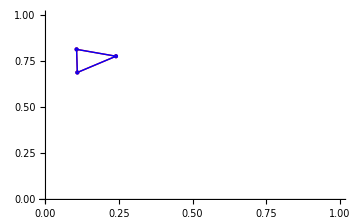

```mathematica
ClearAll[quadrules,n,np]
quadrules={LegendreRule[20,0,1],LegendreRule[3,0,1]};
{n,np}={1,1};
Show[
  ListPlot[pt[[n]], ImageSize -> Medium, PlotStyle -> {Red, PointSize[Large]}, PlotRange -> {{0, 1}, {0, 1}}, Epilog -> {Red, Line[pt[[n]]], Line[{pt[[n, 3]], pt[[n, 1]]}], Blue, Line[pt[[np]]], Line[{pt[[np, 3]], pt[[np, 1]]}]}],
  ListPlot[pt[[np]], PlotStyle -> {Blue, PointSize[Medium]}]
  ] // Print
rawB=ParallelTable[Bnmnpmp[n,m,np,mp,True,quadrules],{m,-Nd,Nd},{mp,-Nd,Nd}]//ToCmplxPckdArry;
```

```mathematica
ClearAll[x0,y0]
x0=RandomComplex[1+ⅈ,Nm];
y0=rawB.x0;
Dimensions/@{x0,y0}//Print
PackedArrayQ/@{x0,y0}//Print
```

{{101},{101}}

{True,True}

```mathematica
ClearAll[xtf,xsf,ztf,zsf,quadrules]
xtf=x0~Join~ConstantArray[0.0+0.0ⅈ,Nm]//Fourier;
xsf=(gTbl x0)~Join~ConstantArray[0.0+0.0ⅈ,Nm]//Fourier;
quadrules={LegendreRule[20,0,1],LegendreRule[3,0,1]};
ztf=Table[BtBandArcSinhMethod[n,np,Δm,quadrules],{Δm,0,2Nd}]~Join~{0.0+0.0ⅈ}~Join~Table[BtBandArcSinhMethod[n,np,Δm,quadrules],{Δm,-2Nd,-1}]//ToCmplxPckdArry//Fourier;
zsf=Table[BsBandArcSinhMethod[n,np,Δm,quadrules],{Δm,0,2Nd}]~Join~{0.0+0.0ⅈ}~Join~Table[BsBandArcSinhMethod[n,np,Δm,quadrules],{Δm,-2Nd,-1}]//ToCmplxPckdArry//Fourier;
y=√(2Nm)InverseFourier[ztf xtf+zsf xsf]⟦1;;Nm⟧;
Dimensions/@{xtf,xsf,ztf,zsf,y}//Print
PackedArrayQ/@{xtf,xsf,ztf,zsf,y}//Print
Print["Max relative err=",(y-y0)/y0//Abs//Max];
```

{{202},{202},{202},{202},{101}}

{True,True,True,True,True}

Max relative err=3.89952×10^-15

Do the same test of FFT on near-singular-blocks

```mathematica
ClearAll[n,m,np,mp,quadrules]
{n,m,np,mp}={1,14,120,30};
quadrules={LegendreRule[15,0,1],LegendreRule[3,0,1]};
raw=Bnmnpmp[n,m,np,mp,True,quadrules]
BtBandArcSinhMethod[n,np,m-mp,quadrules]+BsBandArcSinhMethod[n,np,m-mp,quadrules]gTbl⟦mp+Nd+1⟧
```

-2.93362×10^-7-5.77309×10^-7 ⅈ

-2.93362×10^-7-5.77309×10^-7 ⅈ

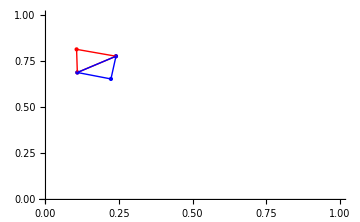

```mathematica
ClearAll[quadrules,n,np]
quadrules={LegendreRule[30,0,1],LegendreRule[3,0,1]};
{n,np}={1,2};
Show[
  ListPlot[pt[[n]], ImageSize -> Medium, PlotStyle -> {Red, PointSize[Large]}, PlotRange -> {{0, 1}, {0, 1}}, Epilog -> {Red, Line[pt[[n]]], Line[{pt[[n, 3]], pt[[n, 1]]}], Blue, Line[pt[[np]]], Line[{pt[[np, 3]], pt[[np, 1]]}]}],
  ListPlot[pt[[np]], PlotStyle -> {Blue, PointSize[Medium]}]
  ] // Print
```

```mathematica
rawB=ParallelTable[Bnmnpmp[n,m,np,mp,True,quadrules],{m,-Nd,Nd},{mp,-Nd,Nd}]//ToCmplxPckdArry;
```

```mathematica
ClearAll[x0,y0]
x0=RandomComplex[1+ⅈ,Nm];
y0=rawB.x0;
Dimensions/@{x0,y0}//Print
PackedArrayQ/@{x0,y0}//Print
```

{{101},{101}}

{True,True}

```mathematica
ClearAll[xtf,xsf,ztf,zsf,quadrules]
xtf=x0~Join~ConstantArray[0.0+0.0ⅈ,Nm]//Fourier;
xsf=(gTbl x0)~Join~ConstantArray[0.0+0.0ⅈ,Nm]//Fourier;
quadrules={LegendreRule[30,0,1],LegendreRule[3,0,1]};
ztf=Table[BtBandArcSinhMethod[n,np,Δm,quadrules],{Δm,0,2Nd}]~Join~{0.0+0.0ⅈ}~Join~Table[BtBandArcSinhMethod[n,np,Δm,quadrules],{Δm,-2Nd,-1}]//ToCmplxPckdArry//Fourier;
zsf=Table[BsBandArcSinhMethod[n,np,Δm,quadrules],{Δm,0,2Nd}]~Join~{0.0+0.0ⅈ}~Join~Table[BsBandArcSinhMethod[n,np,Δm,quadrules],{Δm,-2Nd,-1}]//ToCmplxPckdArry//Fourier;
y=√(2Nm)InverseFourier[ztf xtf+zsf xsf]⟦1;;Nm⟧;
Dimensions/@{xtf,xsf,ztf,zsf,y}//Print
PackedArrayQ/@{xtf,xsf,ztf,zsf,y}//Print
Print["Max relative err=",(y-y0)/y0//Abs//Max];
```

{{202},{202},{202},{202},{101}}

{True,True,True,True,True}

Max relative err=9.04792×10^-15

## New Solver

First, compute the new input vector accurately using 1-point testing and multi-point source

```mathematica
ClearAll[VscnmFunc,VscnmFuncR]
VscnmFunc[m_,r_,rp_]:=Module[{dr,R,r2rphi},
dr=r-rp;R=Norm[dr];If[R<1.0*10^-13,r2rphi=0.0;,r2rphi=ArcTan[dr⟦1⟧,dr⟦2⟧];];
(*Exp[-ⅈ m r2rphi]/R*mus[rp]*PhaseFunc[r2rphi-phis]*Exp[-OpticalPathC[rp,phis+π]]*)
Exp[-ⅈ m r2rphi]/R*mus[rp]*PhaseFunc[r2rphi-phis]*Exp[-rp⟦1⟧]
]
VscnmFuncR[m_,r_,rp_]:=Module[{dr,r2rphi},
dr=r-rp;If[Norm[dr]<1.0*10^-13,r2rphi=0.0;,r2rphi=ArcTan[dr⟦1⟧,dr⟦2⟧];];
(*Exp[-ⅈ m r2rphi]*mus[rp]*PhaseFunc[r2rphi-phis]*Exp[-OpticalPathC[rp,phis+π]]*)
Exp[-ⅈ m r2rphi]*mus[rp]*PhaseFunc[r2rphi-phis]*Exp[-rp⟦1⟧]
]

ClearAll[NpField,VscnmNew]
NpField[P_,m_,QUADRULES_]:=Module[{n,ruleFar,ruleNear,mask,partialIntegral},
mask=Table[Norm[P-cntr⟦n⟧]>0.3,{n,Ns}];
partialIntegral=Table[
If[mask⟦i⟧,
(*Far Field*)NIntegrateTriangleDunavantMethod[pt⟦i⟧,VscnmFunc[m,P,#]&,QUADRULES⟦1⟧],
(*Near Field*)NIntegrateTriangleArcSinh2[P,pt⟦i⟧,VscnmFuncR[m,P,#]&,QUADRULES⟦2⟧]
]*area⟦i⟧
,{i,Ns}];
partialIntegral//Total
]

VscnmNew[n_,m_,QUADRULES_]:=area⟦n⟧NpField[cntr⟦n⟧,3,QUADRULES]
```

```mathematica
ClearAll[VscNEW,n,m,QUADRULES]
QUADRULES={DunavantRule[12,{{0,0},{0,1},{1,0}}],{LegendreRule[15,0,1],LegendreRule[3,0,1]}};
{n,m}={1,0};
(VscNEW=ParallelTable[VscnmNew[n,m,QUADRULES],{n,Ns},{m,-Nd,Nd}]//Flatten//ToCmplxPckdArry;)//AbsoluteTiming//#⟦1⟧&
```

1693.87549

```mathematica
SetDirectory[NotebookDirectory[]]
Export["VscNEW.re.dat",VscNEW//Re]
Export["VscNEW.im.dat",VscNEW//Im]
ResetDirectory[]
```

/Users/qzmfrank/Codes/rte2dvis/notebook

VscNEW.re.dat

VscNEW.im.dat

/Users/qzmfrank

```mathematica
VscnmNew[4,0,QUADRULES]
VscnmNew[4,2,QUADRULES]
```

0.0000109155+2.24672×10^-6 ⅈ

0.0000109155+2.24672×10^-6 ⅈ